```mathematica
a={{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,0}};
(*Choosing node 1 to be excited*)
ρ0={{1},{0},{0},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
state//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ρ0//MatrixForm
```

(1
0
0
0)

```mathematica
(*Defining the time-evolution operator*)
U[t_]:=MatrixExp[a*-ⅈ*t]
```

```mathematica
U[0.5].ConjugateTranspose[U[0.5]]//Chop//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

```mathematica
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
```

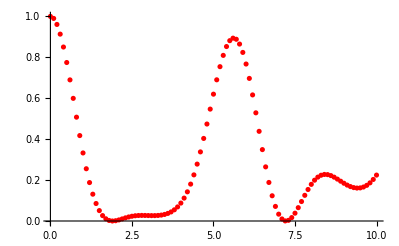

```mathematica
(*Investigating the probability of the state remaining with a single-excitation in the first node*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.1}];
plot1=ListPlot[plot1values,PlotStyle->Red]
```

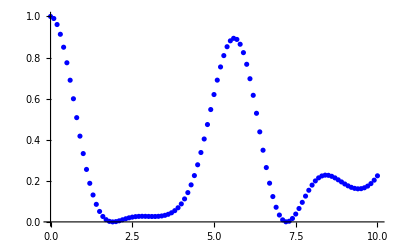

```mathematica
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.1}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
```

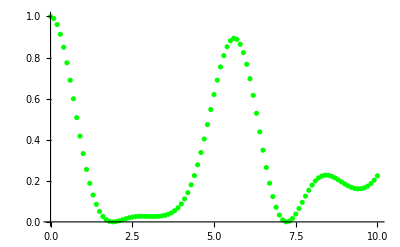

```mathematica
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.1}];
plot3=ListPlot[plot1values,PlotStyle->Green]
```

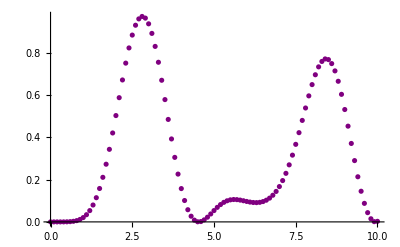

```mathematica
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.1}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

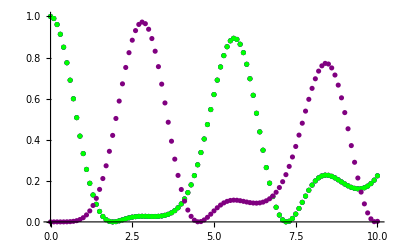

```mathematica
Show[plot1,plot2,plot3,plot4]
```

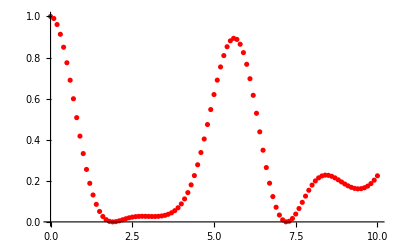

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Choosing node 2 to be excited*)
ρ0={{1},{0},{0},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state remaining with a single-excitation in the second node*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.1}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.1}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.1}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.1}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

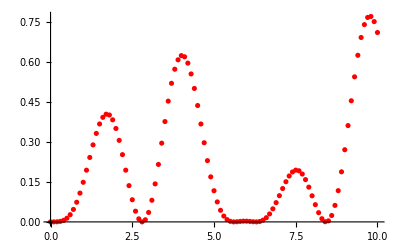

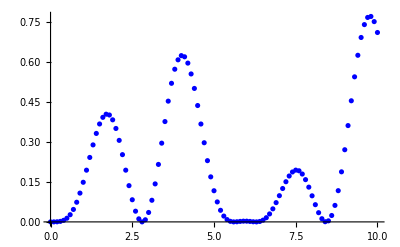

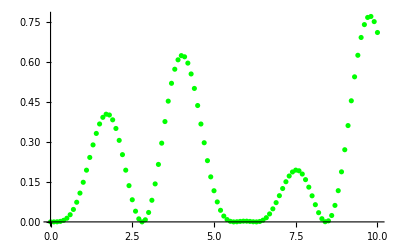

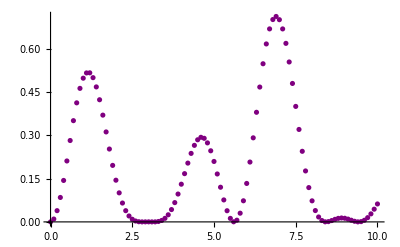

```mathematica
(*Choosing node 3 to be excited*)
ρ0={{0},{0},{1},{0}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state remaining with a single-excitation in the third node*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.1}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.1}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.1}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.1}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```

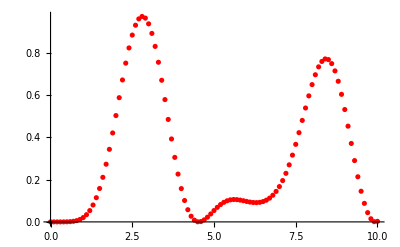

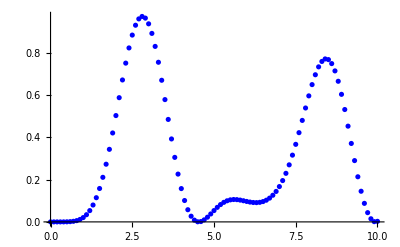

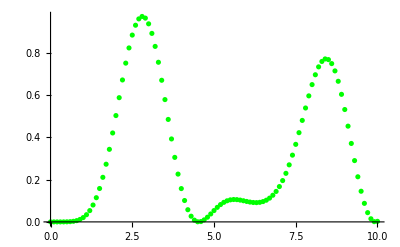

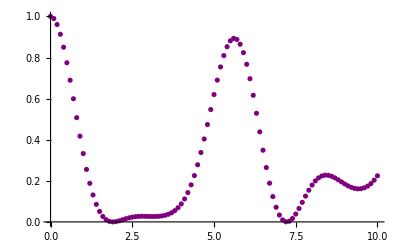

```mathematica
(*Choosing node 4 to be excited*)
ρ0={{0},{0},{0},{1}};
state=KroneckerProduct[ρ0,ConjugateTranspose[ρ0]];
(*Defining the evolution of the state*)
ρ1[t_]:=U[t].state.ConjugateTranspose[U[t]]
(*Investigating the probability of the state remaining with a single-excitation in the fourth node*)
plot1values=Table[{t,ρ1[t][[1,1]]},{t,0,10,0.1}];
plot1=ListPlot[plot1values,PlotStyle->Red]
plot2values=Table[{t,ρ1[t][[2,2]]//N},{t,0,10,0.1}];
plot2=ListPlot[plot1values,PlotStyle->Blue]
plot3values=Table[{t,ρ1[t][[3,3]]},{t,0,10,0.1}];
plot3=ListPlot[plot1values,PlotStyle->Green]
plot4values=Table[{t,ρ1[t][[4,4]]},{t,0,10,0.1}];
plot4=ListPlot[plot4values,PlotStyle->Purple]
```